# Taylor series for the functions

```mathematica
Clear["Global`*"]
```

## Definition

```mathematica
Series[f[x],{x,a,4}]//TraditionalForm
```

f(a)+(x-a) f'(a)+1/2 (x-a)^2 f''(a)+1/6 f^(3)(a) (x-a)^3+1/24 f^(4)(a) (x-a)^4+O((x-a)^5)

## Taylor series for the function at a=0

```mathematica
f[x_]:=Sin[x]
```

```mathematica
(*
Sin[x]
Cos[x]
1/(1-x)
Log[x]
ⅇ^x
xⅇ^x
ArcTan[x]
*)
```

```mathematica
a:=0
```

```mathematica
nb:=5
```

```mathematica
s=Series[f[x],{x,a,nb}]
```

x-x^3/6+x^5/120+O[x]^6

```mathematica
Normal[s]
```

x-x^3/6+x^5/120

```mathematica
Table[SeriesCoefficient[f[x],{x,0,nb}],{nb,0,nb}]
```

{0,1,0,-1/6,0,1/120}

## Presentation

```mathematica
p1:=Plot[f[x],{x,-6,6}]
```

```mathematica
p2:=Plot[Evaluate[Normal[s]],{x,-6,6},PlotStyle->Directive[Red]]
```

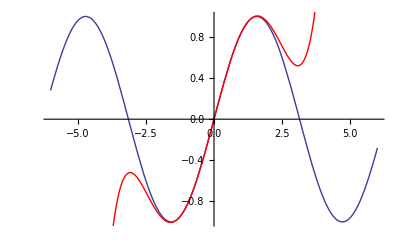

```mathematica
Show[p1,p2]
```